```mathematica
(*longks={{0,0},{1,0},{0,1},{2,0},{1,1},{0,2},{3,0},{2,1},{1,2},{0,3},{4,0},{3,1},{2,2},{1,3},{0,4},{5,0},{4,1},{3,2},{2,3},{1,4},{0,5},{6,0},{5,1},{4,2},{3,3},{2,4},{1,5},{0,6},{7,0},{6,1},{5,2},{4,3},{3,4},{2,5},{1,6},{0,7},{7,1},{6,2},{5,3},{3,5},{2,6},{1,7},{7,2},{6,3},{3,6},{2,7},{7,3},{3,7}};
<<ToMatlab`
Table[SetPrecision[momRRd[longks[[i,1]],longks[[i,2]]],40],{i,1,Length[longks]}]//ToMatlab;*)
```

```mathematica
ClearAll["Global`*"];
(* Upper limit: 
{X, 1, 0.25, 0.101, 0.0211, 0.00625} 
*)
(*rmins={10^-6,10^-6,0.001,0.1,0.1,0.1,0.1};*)
(*rmins=10^-12{1,1,1,1};*)
rmins={0,0,0.2,0.1,0.005};
orthog[m_,n_,dum_]:=
Module[{nn=n,mm=m,σ,a,b,Ja,w,xi,eval,evec,esys},
σ=Table[0.,{i,1,2nn},{j,1,2nn}];
Do[σ[[2,i+1]]=mm[[i+1]],{i,0,2nn-1}];

a=Table[0.,{i,1,nn}];b=a;
a[[1]]=mm[[2]]/mm[[1]];
b[[1]]=0;

Do[
Do[
σ[[i+2,j+1]]=σ[[i+1,j+2]]-a[[i]]σ[[i+1,j+1]]-b[[i]]σ[[i,j+1]];
a[[i+1]]=-σ[[i+1,i+1]]/σ[[i+1,i]]+σ[[i+2,i+2]]/σ[[i+2,i+1]];
b[[i+1]]=σ[[i+2,i+1]]/σ[[i+1,i]];
,{j,i,2nn-i-1}];
,{i,1,nn-1}];

Ja=DiagonalMatrix[a];
Do[
Ja[[i,i+1]]=-Sqrt[Abs[b[[i+1]]]];
Ja[[i+1,i]]=-Sqrt[Abs[b[[i+1]]]];
,{i,1,nn-1}];

esys=Eigensystem[Ja];
eval=esys[[1]];evec=esys[[2]];

w=Table[evec[[i,1]]^2 mm[[1]],{i,1,nn}];
{eval,w,Length[w]}
];
(*orthog[m_,n_,mins_]:=
Module[{nn=n,mom=m,rmin=mins[[1;;n]],eabs=10^-10,σ,a,b,Ja,w,x,xi,eval,evec,esys,myn,ind,nu,nout,cutoff,dab,mab,bmin,z,mindab,maxmab},
(* rmin is minimum ratio wmin/wmax *)
(* eabs is minimum distance between distinct abscissas *)
cutoff=0.;
If [mom[[1]]<0,
Print["Negative number density"];
Abort[];
];
If[mom[[1]]==0,
w=0.;
x=0.;
Return[{{x},{w},1},Module];
];
If[nn==1||mom[[1]]<rmin[[1]],
w=mom[[1]];
x=mom[[2]]/mom[[1]];
Return[{{x},{w},1},Module];
];

(* Compute modified moments equal to moments *)
nu=mom;
(* Construct recurrence matrix *)
ind=nn;
a=Table[0.,{i,ind}];
b=Table[0.,{i,ind}];
σ=Table[0.,{i,2ind+1},{j,2ind+1}];
Do[
σ[[2,i]]=nu[[i-1]];
,{i,2,2ind+1}];
a[[1]]=nu[[2]]/nu[[1]];
b[[1]]=0;
Do[
Do[
σ[[k,l]]=σ[[k-1,l+1]]-a[[k-2]]σ[[k-1,l]]-b[[k-2]]σ[[k-2,l]];
,{l,k,2ind-k+3}];
a[[k-1]]=σ[[k,k+1]]/σ[[k,k]]-σ[[k-1,k]]/σ[[k-1,k-1]];
b[[k-1]]=σ[[k,k]]/σ[[k-1,k-1]];
,{k,3,ind+1}];
(* Determine maximum n using diag elements of sig *)
myn=nn;
Do[
If[Im[σ[[k,k]]]≠0,Print["Imag sig"];(*Print[σ];*)Print[mom];Abort[];];
If[σ[[k,k]]≤cutoff,
myn=k-2;
If[myn==1,
w=mom[[1]];
x=mom[[2]]/mom[[1]];
Return[{{x},{w},1},Module];
];
];
,{k,ind+1,3,-1}];

(* Compute quadrature using maximum n *)
a=Table[0,{i,myn}];
b=Table[0,{i,myn}];
w=Table[0,{i,myn}];
x=Table[0,{i,myn}];
σ=Table[0,{i,2 myn+1},{j,2myn+1}];
Do[
σ[[2,i]]=nu[[i-1]];
,{i,2,2 myn+1}];
a[[1]]=nu[[2]]/nu[[1]];
b[[1]]=0.;
Do[
Do[
σ[[k,l]]=σ[[k-1,l+1]]-a[[k-2]] σ[[k-1,l]]-b[[k-2]] σ[[k-2,l]];
,{l,k,2 myn-k+3}];
a[[k-1]]=σ[[k,k+1]]/σ[[k,k]]-σ[[k-1,k]]/σ[[k-1,k-1]];
b[[k-1]]=σ[[k,k]]/σ[[k-1,k-1]];
,{k,3,myn+1}];
(* Check if moments are not realizable (should never happen) *)
bmin=Min[b];
If[bmin<0,Print["Moments in Wheeler moments are not realizable!"];Abort[];];
(* Setup Jacobi matrix for n-point quadrature, adapt n using rmax and eabs *)
Do[
If[nl==1,
w=mom[[1]];
x=mom[[2]]/mom[[1]];
Return[{{x},{w},1},Module];
];
z=Table[0,{i,1,nl},{j,1,nl}];
Do[
z[[i,i]]=a[[i]];
z[[i,i+1]]=Sqrt[b[[i+1]]];
z[[i+1,i]]=z[[i,i+1]];
,{i,1,nl-1}];
z[[nl,nl]]=a[[nl]];
(* Compute weights and abscissas *)
esys=Eigensystem[z];
eval=esys[[1]];evec=esys[[2]];
w=Table[0,{i,1,nl}];
x=w;
dab=w;
mab=w;
x=eval;
w=Table[evec[[i,1]]^2 mom[[1]],{i,1,nl}];
Do[
dab[[i]]=Min[Abs[x[[i]]-x[[1;;i-1]]]];
mab[[i]]=Max[Abs[x[[i]]-x[[1;;i-1]]]];
,{i,nl,2,-1}];
mindab=Min[dab[[2;;nl]]];
maxmab=Max[mab[[2;;nl]]];
If[nl==2,
maxmab=1;
];
(* Check conditions that weights and abscissas must both satisfy *)
If[Im[{Min[w],Max[w],mindab,maxmab}]≠0,Print["Imaginary part"];Abort[];];
If[
Min[w]/Max[w]>rmin[[nl]]&&mindab/maxmab>eabs,
If[Min[w]<0||Norm[Im[w]]>0,Print["Neg. weight in wheeler"];Abort[];];
If[Norm[Im[x]]>0,Print["Imag. abscissas"];Abort[];];
Return[{x,w,Length[w]},Module];
(*,
Print["ws: ",w];
Print["xs: ",x];
Abort[];*)
];
,{nl,myn,1,-1}];
];*)
```

```mathematica
(* Physical parameters *)
(* lin *)
(*Ca=1;Cp=-1;γ=1;Rey=10 10^6;*)
(*γ=1/2;Rey=4;*)
(*Ca=1/2;Cp=0;γ=1;Rey=Infinity;*)
(* nonlin *)
Ca=1/2;Cp=1/0.5;γ=1;Rey=300;S=30;

μR=1.;
σR=0.1;(* broader distributions -> can use more points *)
μRd=10^-14;
σRd=0.02;
(*ρRRd=0.;*)
(*RRdPDF=BinormalDistribution[{μR,μRd},{σR,σRd},0];*)

𝒟r=LogNormalDistribution[Log[μR],σR];
𝒟v=NormalDistribution[μRd,σRd];
RRdPDF=ProductDistribution[𝒟r,𝒟v];

momRRd[i_,j_]:=Moment[RRdPDF,{i,j}];

nr=2;
nrd=2;
k1=Flatten[{Table[{q,p},{q,0,nr-1},{p,0,2nrd-1}],
Table[{q,p},{q,nr,2nr-1},{p,0,0}]}
,2];
k2=Table[{k1[[i,2]],k1[[i,1]]},{i,1,Length[k1]}];
k2=Flatten[{
Table[{p,q},{q,0,nrd-1},{p,0,2nr-1}],
Table[{p,q},{q,nrd,2nrd-1},{p,0,0}]}
,2];
ks=DeleteDuplicates[Join[k1,k2]];
ksp={{3,0},{2,1},{3,2},{3(1-γ),0}};

project1[xi_,xis_,w_,ws_,nnr_,nnrd_]:=Module[{moms,mom,wtot,momsp},
Do[wtot[j,i]=w[[j]]ws[j][[i]],{j,1,nnr},{i,1,nnrd[j]}];
mom[p_,q_]:=Sum[wtot[j,i] xi[[j]]^p(xis[j][[i]])^q,{j,1,nnr},{i,1,nnrd[j]}];
moms=Table[mom[ks[[i,1]],ks[[i,2]]],{i,1,Length[ks]}];
momsp=Table[mom[ksp[[i,1]],ksp[[i,2]]],{i,1,Length[ksp]}];
{moms,momsp}
];

project2[xi_,xis_,w_,ws_,nnr_,nnrd_]:=Module[{moms,mom,wtot,momsp},
Do[wtot[j,i]=w[[j]]ws[j][[i]],{j,1,nnrd},{i,1,nnr[j]}];
mom[p_,q_]:=Sum[wtot[j,i] xi[[j]]^q(xis[j][[i]])^p,{j,1,nnrd},{i,1,nnr[j]}];
moms=Table[mom[ks[[i,1]],ks[[i,2]]],{i,1,Length[ks]}];
momsp=Table[mom[ksp[[i,1]],ksp[[i,2]]],{i,1,Length[ksp]}];
{moms,momsp}
];

myrhs[momin_]:=
Module[{moms=momin,momout1,momout2,momout,rhs1,rhs2,rhs,momsp1,momsp2},
(* converts vector of total M_lmn to M_lm @ each R_o,k *)
eqns=Table[moms[[i]]==pm[ks[[i,1]],ks[[i,2]]],{i,1,Length[ks]}];
vars=DeleteDuplicates[Flatten[Table[pm[ks[[i,1]],ks[[i,2]]],{i,1,Length[ks]}]]];
linsolv=First[vars/.Solve[eqns,vars]];
If[Norm[Im[moms]]>0,Print["Imag moments!"];];
(* moment map *)
mymom[q_,p_]:=linsolv[[First[First[Position[ks,{q,p}]]]]];

ClearAll[nnr,nnrd];
(* conditioning on R-direction *)
(* get unconditioned moments *)
mRs=Table[mymom[i,0],{i,0,2nr-1}];
If[Norm[Im[mRs]]>0,Print["Imag momvec 1"];];
{xi,w,nnr}=orthog[mRs,nr,rmins];
v=Table[Table[xi[[i]]^j,{i,1,nnr}],{j,0,nnr-1}];
r1=DiagonalMatrix[w];
Do[ms[i]=Table[mymom[j,i],{j,0,nnr-1}],{i,0,2nrd-1}];
Do[condmoms[i]=Re[LinearSolve[v.r1,ms[i]]],{i,0,2nrd-1}];
Do[
condmomvec[j]=Table[condmoms[i][[j]],{i,0,2nrd-1}];
If[Norm[Im[condmomvec[j]]]>0,Print["Imag cond momvec"];];
,{j,1,nnr}];

Do[
{xis[i],ws[i],nnrd[i]}=orthog[condmomvec[i],nrd,rmins];
,{i,1,nnr}];

Do[
wtot[j,i]=w[[j]]ws[j][[i]];
If[Re[wtot[j,i]]<0||Im[wtot[j,i]]≠0,Print["Negative weights"];Abort[];];
,{j,1,nnr}
,{i,1,nnrd[j]}];

(* note that in mom[p,q,l], l is the Ro index and p and q are moment exponents! *)
momtot[p_,q_]:=Sum[wtot[j,i] xi[[j]]^p(xis[j][[i]])^q,{j,1,nnr},{i,1,nnrd[j]}];
rhs1={};
Do[
l=ks[[i,1]];
m=ks[[i,2]];
AppendTo[rhs1,
(*l momtot[l-1,m+1]-m(4/Rey momtot[l,m]+2 γ Ca momtot[l+1,m-1]+Cp momtot[l,m-1])*)
l momtot[l-1,m+1]+m(momtot[l-1-3γ,m-1]-3/2 momtot[l-1,m+1]-Cp momtot[l-1,m-1](*-(4/Rey) momtot[l-2,m]+2/S(momtot[l-1-3γ,m-1]-momtot[l-2,m-1])*))
];
,{i,1,Length[ks]}];
{momout1,momsp1}=project1[xi,xis,w,ws,nnr,nnrd];
nnodes1=Sum[nnrd[j],{j,1,nnr}];

ClearAll[nnr,nnrd];
(* conditioning on Rdot-direction *)
(* get unconditioned moments *)
mRds=Table[mymom[0,i],{i,0,2nrd-1}];
If[Norm[Im[mRds]]>0,Print["Imag momvec 2"];];
{xi,w,nnrd}=orthog[mRds,nrd,rmins];

v=Table[Table[xi[[i]]^j,{i,1,nnrd}],{j,0,nnrd-1}];
r1=DiagonalMatrix[w];
Do[ms[i]=Table[mymom[i,j],{j,0,nnrd-1}],{i,0,2nr-1}];
Do[condmoms[i]=Re[LinearSolve[v.r1,ms[i]]],{i,0,2nr-1}];
Do[
condmomvec[j]=Table[condmoms[i][[j]],{i,0,2nr-1}];
If[Norm[Im[condmomvec[j]]]>0,Print["Imag cond momvec"];];
,{j,1,nnrd}];

Do[
{xis[i],ws[i],nnr[i]}=orthog[condmomvec[i],nr,rmins];
,{i,1,nnrd}];

Do[
wtot[j,i]=w[[j]]ws[j][[i]];
If[Re[wtot[j,i]]<0||Im[wtot[j,i]]≠0,Print["Negative weights"];Abort[];];
,{j,1,nnrd}
,{i,1,nnr[j]}];

(* note that in mom[p,q,l], l is the Ro index and p and q are moment exponents! *)
momtot[p_,q_]:=Sum[wtot[j,i] xi[[j]]^q(xis[j][[i]])^p,{j,1,nnrd},{i,1,nnr[j]}];

rhs2={};
Do[
l=ks[[i,1]];
m=ks[[i,2]];
AppendTo[rhs2,
(*l momtot[l-1,m+1]-m(4/Rey momtot[l,m]+2 γ Ca momtot[l+1,m-1]+Cp momtot[l,m-1])*)
l momtot[l-1,m+1]+m(momtot[l-1-3γ,m-1]-3/2 momtot[l-1,m+1]-Cp momtot[l-1,m-1](*-(4/Rey) momtot[l-2,m]+2/S(momtot[l-1-3γ,m-1]-momtot[l-2,m-1])*))
];
If[Norm[Im[rhs2[[i]]]]>0,Print["imag",i," rhs: "];Print[{l-1-3γ,momtot[l-1-3γ,m-1]}];Abort[];];
,{i,1,Length[ks]}];
{momout2,momsp2}=project2[xi,xis,w,ws,nnr,nnrd];
nnodes2=Sum[nnr[j],{j,1,nnrd}];

momout=Total[{momout1,momout2}]/2;
momsp=Total[{momsp1,momsp2}]/2;
rhs=Total[{rhs1,rhs2}]/2;

If[Norm[Im[rhs1]]>0,Print["Imag RHS1"];Abort[];];
If[Norm[Im[rhs2]]>0,Print["Imag RHS2"];Print[{w,ws[1],ws[2],ws[3]}];Abort[];];
If[Norm[Im[momout]]>0,Print["Imag momout"];];
(*diff=Norm[moms-momout];
If[diff>10^-8,Print["Projection error: ",diff]];*)
{momout,rhs}
];
```

```mathematica
dt0=1 10^-5;
dt=dt0;
dtmin=dt ;
dtmax=100000dt0;
(*Nt=10000;*)
(*T=3;*)
Nperiod=1;
T=Nperiod 3.4(1/Cp)^0.75;
tol=1 10^-5;

(*c[1]=37/378;c[2]=0;c[3]=250/621;c[4]=125/594;c[5]=0;c[6]=512/1771;
cs[1]=2825/27648;cs[2]=0;cs[3]=18575/48384;cs[4]=13525/55296;cs[5]=277/14336;cs[6]=1/4;

b0[2,1]=1/5;
b0[3,1]=3/40;b0[3,2]=9/40;
b0[4,1]=3/10;b0[4,2]=-(9/10);b0[4,3]=6/5;
b0[5,1]=-(11/54);b0[5,2]=5/2;b0[5,3]=-(70/27);b0[5,4]=35/27;
b0[6,1]=1631/55296;b0[6,2]=175/512;b0[6,3]=575/13824;b0[6,4]=44275/110592;b0[6,5]=253/4096;*)

(* SSP RK(5,4) coefficients *)
(*c[1,0]=1;c[1,1]=0.391752226571890;
c[2,0]=0.444370493651235;c[2,1]=0.555629506348765;c[2,2]=0.368410593050371;
c[3,0]=0.620101851488403;c[3,1]=0.379898148511597;c[3,2]=0.251891774271694;
c[4,0]=0.178079954393132;c[4,1]=0.821920045606868;c[4,2]=0.544974750228521;
c[5,0]=0.517231671970585;c[5,1]=0.096059710526147;c[5,2]=0.063692468666290;c[5,3]=0.386708617503269;
c[5,4]=0.226007483236906;*)

(* gets total moments in {lmn} from conditional moments on {lm} plus Ro directions *)
ic=Table[momRRd[ks[[i,1]],ks[[i,2]]],{i,1,Length[ks]}];
moms=ic;

sol={};ts={};dets={};abscissa={};spsol={};nodes={};
t=0;
Monitor[While[t≤T,
If[t==0,{moms,rhs}=myrhs[moms]];

(*(* Euler step *)
momstemp1=moms+dt rhs;
{momstemp1,rhs}=myrhs[momstemp1];
mome=momstemp1;
(* SSP-RK2 *)
moms=(1/2) moms+(1/2)(momstemp1+dt rhs);
{moms,rhs}=myrhs[moms];*)

(* SSP-RK2 *)
(*{moms,rhs}=myrhs[moms];*)
momstemp1=moms+dt rhs;
{momstemp1,rhs}=myrhs[momstemp1];
mome=(1/2) moms+(1/2)(momstemp1+dt rhs);
{mome,dummy}=myrhs[mome];

(* SSP-RK3 *)
momstemp2=(3/4)moms+(1/4)(momstemp1+dt rhs);
{momtemp2,rhs}=myrhs[momstemp2];
moms=(1/3)moms+(2/3)(momtemp2+dt rhs);
{moms,rhs}=myrhs[moms];

(*(* SSP-RK3/4 *)
momstemp1=moms+dt rhs;
{momstemp1,rhs}=myrhs[momstemp1];
momstemp2=(3/4)moms+(1/4)(momstemp1+dt rhs);
{momtemp2,rhs}=myrhs[momstemp2];
mome=(1/3)moms+(2/3)(momtemp2+dt rhs);
{mome,rhs}=myrhs[mome];

{moms,rhs}=myrhs[moms];
momstemp1=c[1,0]moms+c[1,1]dt rhs;
{momstemp1,rhs}=myrhs[momstemp1];
momstemp2=c[2,0]moms+c[2,1] momstemp1+c[2,2] dt rhs;
{momstemp2,rhs}=myrhs[momstemp2];
momstemp3=c[3,0]moms+c[3,1]momstemp2+c[3,2]dt rhs;
{momstemp3,rhs3}=myrhs[momstemp3];
momstemp4=c[4,0]moms+c[4,1]momstemp3+c[4,2] dt rhs3;
{momstemp4,rhs4}=myrhs[momstemp4];
moms=c[5,0]momstemp2+c[5,1]momstemp3+c[5,2]dt rhs3+c[5,3]momstemp4+c[5,4]dt rhs4;
{moms,rhs}=myrhs[moms];*)

e=Norm[(moms-mome)/moms];

(* Embedded SSPRK32 from Gottleib, Ketchesen, Chu [doesn't work at all] *)
(*{moms,rhs}=myrhs[moms];
momstemp1=moms+(dt/2) rhs;
{momstemp1,rhs}=myrhs[momstemp1];
momstemp2=momstemp1+(dt/2)rhs;
{momstemp2,rhs}=myrhs[momstemp2];
mome=(1/3) moms+(2/3)(momstemp2+dt rhs);
momstemp3=(2/3) moms+(1/3)(momstemp2+dt rhs);
{momtemp3,rhs}=myrhs[momstemp3];
moms=momstemp3+(dt/2)rhs;*)

(* Four-stage SSP-RK3 *)
(*moms=moms0;
{moms,rhs}=myrhs[moms];
momstemp1=(1/2)moms+(1/2)(moms+dt rhs);
{momtemp1,rhs}=myrhs[momstemp1];
momstemp2=(1/2)momstemp1+(1/2)(momstemp1+dt rhs);
{momtemp2,rhs}=myrhs[momstemp2];
momstemp3=(2/3)moms+(1/6)momstemp2+(1/6)(momstemp2+dt rhs);
{momstemp3,rhs}=myrhs[momstemp3];
moms=(1/2)momstemp3+(1/2)(momstemp3+dt rhs);*)

(* Fifth-order RK *)
(*Do[b[i,j]=dt b0[i,j],{i,1,6},{j,1,6}];
{mtemp[1],myk[1]}=myrhs[moms];
{mtemp[2],myk[2]}=myrhs[mtemp[1]+b[2,1] myk[1]];
{mtemp[3],myk[3]}=myrhs[mtemp[2]+b[3,1] myk[1]+b[3,2] myk[2]];
{mtemp[4],myk[4]}=myrhs[mtemp[3]+b[4,1] myk[1]+b[4,2] myk[2]+b[4,3] myk[3]];
{mtemp[5],myk[5]}=myrhs[mtemp[4]+b[5,1] myk[1]+b[5,2] myk[2]+b[5,3] myk[3]+b[5,4] myk[4]];
{mtemp[6],myk[6]}=myrhs[mtemp[5]+b[6,1] myk[1]+b[6,2] myk[2]+b[6,2] myk[3]+b[6,4] myk[4]+b[6,5] myk[5]];

moms=mtemp[6]+dt Sum[c[i] myk[i],{i,1,6}];
e=Norm[dt Sum[(c[i]-cs[i])myk[i],{i,1,6}]];*)

(* permutation 1 *)
(*AppendTo[abscissa,Table[Thread[{xi[[i]],xis[i]}],{i,1,nnr}]];*)
(* permutation 2 *)
AppendTo[abscissa,Table[Thread[{xis[i],xi[[i]]}],{i,1,nnrd}]];
AppendTo[spsol,momsp];
AppendTo[sol,moms];
AppendTo[ts,t];
AppendTo[nodes,{nnodes1,nnodes2}];

t=t+dt;
dt=Min[Max[0.9 dt Min[Max[Sqrt[tol/(2 e)],0.3],2.],dtmin],dtmax];

(*If[Sum[nnrd[i],{i,1,nnr}]≤nr,
Print["Not enough y-dir quadrature points"];
Break[];
];*)
If[Norm[moms]>10^10,
Print["Crash ",100 t/T];
Break[];
];
];
,TableForm[{{"Time",100t/T},{"δt",dt/dt0},{"Moments",Max[Abs[moms]]},{"Nodes",{nnodes1,nnodes2}}}]
];
Length[ts]
```

2574

```mathematica
myn=90;
myts=Table[ts[[i]],{i,1,Length[abscissa],Floor[Length[abscissa]/myn]}];
inx=Table[i,{i,1,Length[abscissa],Floor[Length[abscissa]/myn]}];
myabscissa=Table[abscissa[[i]],{i,1,Length[abscissa],Floor[Length[abscissa]/N[myn]]}];
xdat=Table[Flatten[myabscissa[[i]],1][[All,1]],{i,1,Length[myabscissa]}];
ydat=Table[Flatten[myabscissa[[i]],1][[All,2]],{i,1,Length[myabscissa]}];
xmax=If[Max[xdat]>0,1.2 Max[xdat],0.8 Max[xdat]];
xmin=If[Min[xdat]<0,1.2 Min[xdat],0.8 Min[xdat]];
ymax=If[Max[ydat]>0,1.2 Max[ydat],0.8 Max[xdat]];
ymin=If[Min[ydat]<0,1.2Min[ydat],0.8 Min[ydat]];
ListAnimate[ParallelTable[
ListPlot[Flatten[myabscissa[[i]],1],PlotStyle->Red,PlotRange->{{xmin,xmax},{ymin,ymax}},AspectRatio->1]
(*ListPlot[Flatten[myabscissa[[i]],1],PlotStyle->Red,PlotRange->{{0,1.9},{-3,3}},AspectRatio->1]*)
,{i,1,Length[myabscissa]}]]
```

```mathematica
plots={};
Do[
If[Total[ks[[i]]]<4&&Total[ks[[i]]]>0,
AppendTo[plots,ListPlot[Thread[{ts,sol[[All,i]]}],Joined->True,PlotRange->All,PlotLabel->ks[[i]]]]
]
,{i,1,Length[moms]}]
plots

plots={};
Do[
AppendTo[plots,ListPlot[Thread[{ts,spsol[[All,i]]}],Joined->True,PlotRange->All,PlotLabel->ksp[[i]]]]
,{i,1,Length[momsp]}]
plots
```

```mathematica
(* Verify with Monte Carlo *)
Ncases=5000;
cases=RandomVariate[RRdPDF,Ncases];
β=2/Rey;ω2= 2 γ Ca;
Clear[t];
(*myr=ParallelTable[
r[t]/.(NDSolve[
{r''[t] == -2 β r'[t]-ω2 r[t]-Cp,r[0]==cases[[i,1]],r'[0]==cases[[i,2]]},
r[t],
{t,0,T}]//First//First),
{i,1,Ncases}];*)
myr=ParallelTable[
r[t]/.(NDSolve[
{r[t]r''[t]+3/2 r'[t]^2 ==(1/r[t])^(3 γ)-Cp,r[0]==cases[[i,1]],r'[0]==cases[[i,2]]},
r[t],
{t,0,T}]//First//First),
{i,1,Ncases}];
mydr=Table[
D[myr[[i]],t],{i,1,Ncases}];

Nt=100;ts2=Table[i,{i,0,T,T/Nt}];
ts2=myts;Nt=Length[ts2];
P=Table[Table[{
myr[[j]]/.{t->ts2[[i]]},
mydr[[j]]/.{t->ts2[[i]]}},{j,1,Ncases}],
{i,1,Nt}];

nonlinmoments=ParallelTable[Table[{ts2[[i]],Moment[P[[i]],ks[[j,1;;2]]]},{i,1,Nt}],{j,1,Length[ks]}];

(*skewR=ParallelTable[{ts2[[i]],Skewness[P[[i]]][[1]]},{i,1,Nt}];
skewRd=ParallelTable[{ts2[[i]],Skewness[P[[i]]][[2]]},{i,1,Nt}];
kurtR=ParallelTable[{ts2[[i]],-3+Kurtosis[P[[i]]][[1]]},{i,1,Nt}];
kurtRd=ParallelTable[{ts2[[i]],-3+Kurtosis[P[[i]]][[2]]},{i,1,Nt}];*)
```

```mathematica
Max[skewR[[All,2]]]
Max[skewRd[[All,2]]]
Max[kurtR[[All,2]]]
Max[kurtRd[[All,2]]]
ListPlot[{skewR,skewRd,kurtR,kurtRd},Joined->True,PlotRange->All]
```

```mathematica
plts=ParallelTable[
Show[
SmoothDensityHistogram[P[[i]],PlotRange->{{xmin,xmax},{ymin,ymax},All}],
ListPlot[Flatten[myabscissa[[i]],1],PlotStyle->Red,PlotRange->{{xmin,xmax},{ymin,ymax}}]]
,{i,1,Length[P]}];
vid=ListAnimate[plts]
```

```mathematica
Export["~/Desktop/nonlinear_3x3_06pratio_0_01std.avi",plts]
```

~/Desktop/nonlinear_3x3_06pratio_0_01std.avi

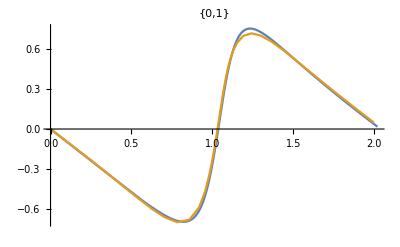
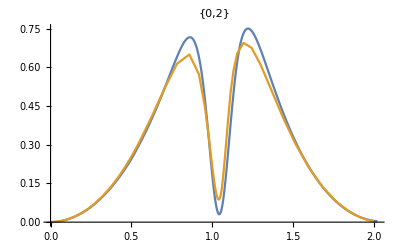
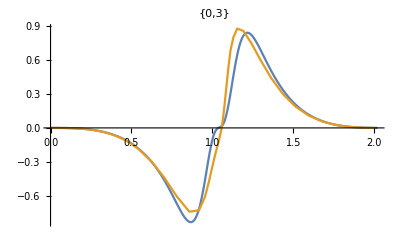
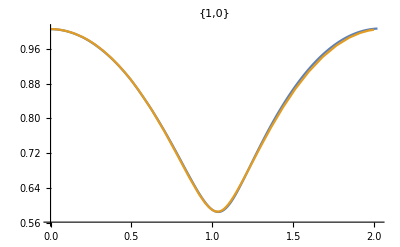
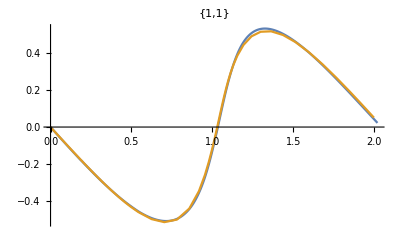
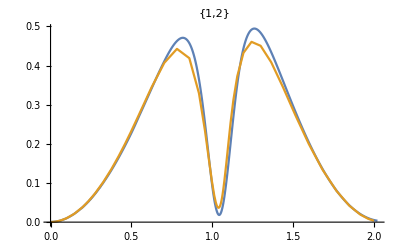
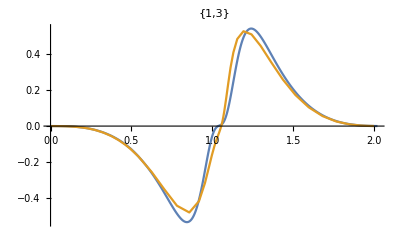
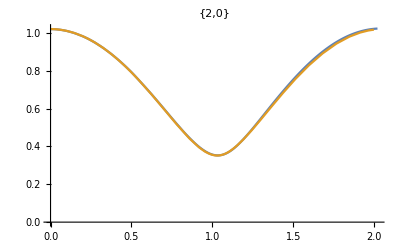

```mathematica
plots={};
Do[
If[Total[ks[[i]]]<10&&Total[ks[[i]]]>0,
AppendTo[plots,ListPlot[{Thread[{ts,sol[[All,i]]}],nonlinmoments[[i]]},Joined->True,PlotRange->All,PlotLabel->ks[[i]]]]
]
,{i,1,Length[moms]}]
plots
```

```mathematica
errors=Table[Max[Abs[Table[sol[[j,i]],{j,inx}]-nonlinmoments[[i,All,2]]]]/Max[Abs[nonlinmoments[[i,All,2]]-nonlinmoments[[i,1,2]]]],{i,2,Length[moms]}]
```

```mathematica
ListLogPlot[errors,PlotRange->All]
```